```mathematica
Clear["Global`*"]
Ca=10^-17;
e=1.602* 10^-19;
EC=e^2/(2*Ca);
kb=1.38* 10^-23;
Vg=0.03;
γL=1000000000;
γR=1000000000;
muD=5.5;
muL=5;
muR=6;
T=3;

fdist[En_,mu_,T_]:=1/(Exp[(En-mu)/(kb*T)]+1);
Nopt[Vg_]:=Floor[e*Vg/(2*EC)];
EN[n_]:=EC*n^2-e*Vg*n;
f[En_]:=En/(Exp[En/(kb*T)]-1);
GamL[n1_,n2_,V_]:=γL*f[EN[n1]-EN[n2]+(n1-n2)*e*V/2];
GamR[n1_,n2_,V_]:=γR*f[EN[n1]-EN[n2]+(n1-n2)*e*V/2];
WE[n1_,n2_,V_]:=GamL[n1,n2,V]+GamR[n1,n2,V];
(*Define scattering probability matrix W*)
Wn[n_,V_]:=SparseArray[{Band[{1,2},{n-1,n},{1,1}]->Table[WE[i,i+1,V],{i,0,n-2}],Band[{1,1},{n,n},{1,1}]->Table[-WE[i+1,i,V]-WE[i-1,i,V],{i,0,n-1}],Band[{2,1},{n,n-1},{1,1}]->Table[WE[i,i-1,V],{i,0,n-2}]},{n,n}];
W[n_,V_]:={{WE[n,n-1,V],0,0},{0,-WE[n+1,n,V]-WE[n-1,n,V],0},{0,0,WE[n,n+1,V]}};
P[V_]:=Table[1,3].(Inverse[W[1,V]+IdentityMatrix[3]])

IL[V_]:=-e*Sum[(GamL[n+1,n,V]-GamL[n-1,n,V])*(P[V])[[2]],{n,1,20}]
```

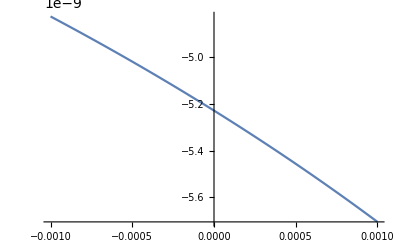

```mathematica
Plot[{N[P[V]][[2]]},{V,-0.001,0.001},PlotRange->All]
```

```mathematica
0
```

```mathematica
Plot[IL[V]/V,{V,-1,1}]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.67239×10^10,0.,0.},{0.,-1.62106×10^10,0.},{0.,0.,1.}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

-Graphics-

```mathematica
GamL[1,2,0.001]
f[EN[5]-EN[6]+(-1)*e*0.01/2]
```

0.0562531

1.01102×10^-20

```mathematica
(EN[5]-EN[6])/(kb*T)
```

-224.86

```mathematica
WE[1,0,0.01]
```

5.4436×10^-12

```mathematica
EC/(kb*T)
```

30.9952

```mathematica
Nopt[0.03]
```

1

{-0.000040707,-0.00197108,-0.00231282,-0.00636793,-0.00962199}

```mathematica
Wn[3,0.01]
```

SparseArray[<7>, {3, 3}]

```mathematica
Normal[%2958]
```

{{-5.4436×10^8,1.5264×10^-20,0},{1.05764×10^9,-3.18246×10^7,745845.},{0,5.4436×10^8,-745845.}}

```mathematica
Normal[%]
```

{{-5.4436,1.5264×10^-28,0},{10.5764,-0.318246,0.00745845},{0,5.4436,-0.00745845}}

```mathematica
Inverse[Wn[3,0.001]+IdentityMatrix[3]]//MatrixForm
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{-6.8854×10^8,5.28837×10^-28,0.},{1.20182×10^9,-1.75259×10^8,0.112506},{0.,6.8854×10^8,0.887494}} may contain significant numerical errors.

(-1.45235×10^-9 | 4.08572×10^-26 | -1.98852×10^-26
-6.64827×10^-9 | -3.80889×10^-9 | 4.82846×10^-10
5.15789 | 2.95503 | 0.752164)

```mathematica
kb*T
```

3/10000000000000000000000000000000000

```mathematica
N[3/10000000000000000000000000000000000]
```

3.×10^-34

```mathematica
NumberForm[P[0.004],20]
```

{1.000000000037166,1.000000000026901,1.000000000016635,1.00000000000637,1.000000000000619,1.,1.}

```mathematica
Total[{1.0000000005421137,1.,1.,1.,1.,1.,1.0000000000000002,1.0000000000000002,1.0000000000000002,1.,1.,1.,1.,1.,1.,1.0000000000000002,1.0000000000000002,1.0000000000000002,1.,1.}]
```

20.

```mathematica
kb*T/EC
```

0.032263

```mathematica
NumberForm[20.000000000542116,16]
```

20.00000000054212

```mathematica
NumberForm[1.,16]
```

1.

```mathematica
NumberForm[1.,16]
```

1.

```mathematica
RealDigits[1.]
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},1}

```mathematica
NumberForm[1.000000000140912,16]
```

1.000000000140912

$Aborted